# Fig. 1

From “Schwarzschild-de Sitter spacetime in regular coordinates with cosmological time” (2025) by L. Lima and D.C. Rodrigues.

Davi C. Rodrigues

```mathematica
SetDirectory[NotebookDirectory[]];

Clear[m, Λ]
Am = A /. Solve[A == 1 - (2 m)/r - r^2 Λ/3(1 - A^-1), A][[1]];
Ap = A /. Solve[A == 1 - (2 m)/r - r^2 Λ/3(1 - A^-1), A][[2]];
f = 1 - 2 m/r -  Λ/3 r^2; 

Echo[Expand[Am],  "Am = A = "];
Echo[Expand[Ap],  "Ap = A = "];
Echo[Expand[f],  "f = "];
```

Am = A =   1/2-m/r-(r^2 Λ)/6-(√(12 r^4 Λ+(6 m-3 r+r^3 Λ)^2))/(6 r)

Ap = A =   1/2-m/r-(r^2 Λ)/6+(√(12 r^4 Λ+(6 m-3 r+r^3 Λ)^2))/(6 r)

f =   1-(2 m)/r-(r^2 Λ)/3

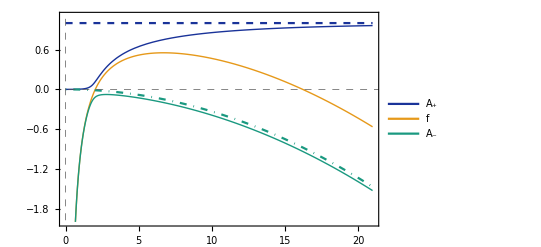

plotAlphas.pdf

```mathematica
m = 1;
Λ = 1/100;

legend = LineLegend[
  {"A_+",  "f", "A_-"},
  LegendFunction-> (Framed[#, RoundingRadius -> 5, FrameStyle-> Thin]&),
  LegendMarkerSize->{{30, 15}}
];
    
plot = Plot[
  {Ap, f,  Am, 1, - Λ/3 r^2}, 
  {r, 0, 21},
  PlotRange-> {Automatic, {-2.0, 1.1}}, 
  PlotTheme->"Scientific",
  Background->White,
  FrameStyle->Directive[Black, 15],
  PlotLegends-> Placed[legend, Scaled[{0.25, 0.27}]],
  LabelStyle->{FontFamily -> "Times", FontSize-> 15},
  PlotStyle -> {
   {RGBColor[0.1, 0.2, 0.6], Thick}, 
   {RGBColor[0.9, 0.6, 0.1], Thick}, 
   {RGBColor[0.1, 0.6, 0.5], Thick},
   {RGBColor[0.1, 0.2, 0.6], Dashed, Thickness[0.004]} ,
   {RGBColor[0.1, 0.6, 0.5], DotDashed, Thickness[0.004]}
  },
  GridLinesStyle->Directive[Darker@Gray, Dashed],
  PlotRangePadding-> 0
]

Export["plotAlphas.pdf", plot]
```